```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["Results/dldw_a1nm_v0.5_b5.5nm_extF2.dat"];
```

```mathematica
data[[3]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_}->{a,n}
```

{w(au),dlEedwx}

```mathematica
dLEedwx=data[[4;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_}->{a,n};
dLHedwx=data[[4;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_}->{a,o};
dLEedwy=data[[4;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_}->{a,p};
dLHedwy=data[[4;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_}->{a,q};
dLEedwz=data[[4;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_}->{a,r};
dLHedwz=data[[4;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_,q_,r_,s_}->{a,s};
```

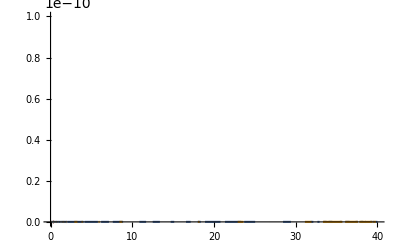

-Graphics-

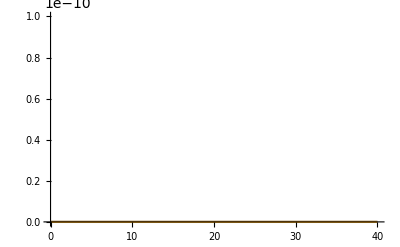

```mathematica
ListPlot[{dLEedwx,dLHedwx}, PlotRange->{{0,40},{0,10^-10}}, Joined->True]
ListPlot[{dLEedwy,dLHedwy}, PlotRange->{{0,40},{0,10^-10}}, Joined->True]
ListPlot[{dLEedwz,dLHedwz}, PlotRange->{{0,40},{0,10^-10}}, Joined->True]
```

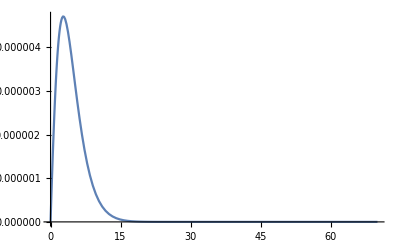

```mathematica
ListPlot[dLHedwx, PlotRange->All, Joined->True]
```

```mathematica
dLHedwx[[700]]
```

{67.5571,0}

```mathematica
dataP=Import["dpdw_a1nm_v0.5_b1.5nm.dat"];
```

```mathematica
dataP[[1]]
```

{w(au),dpEdwx,dpHdwx,dpEdwz,dpHdwz,dpEsdwx,dpHsdwx,dpEsdwz,dpHsdwz,dpEedwx,dpHedwx,dpEedwz,dpHedwz}

```mathematica
dPEedwx=dataP[[2;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_}->{a,j};
dPHedwx=dataP[[2;;]]/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_}->{a,k};
```

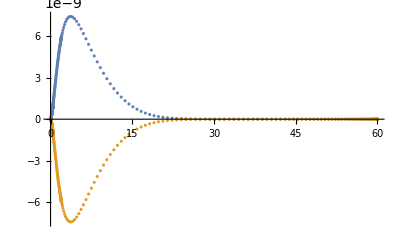

```mathematica
ListPlot[{dPEedwx,dPHedwx}, PlotRange->All]
```

```mathematica
2!!
```

2

```mathematica
c=137.035999139;
nm=100./5.2918;
a=1.0*nm;
r=1.05*nm;
b=1.5*nm;
(*ω=0.1;*)
k[ω_]=ω/c;
v=0.5*c;
γ=1/(√(1-v^2/c^2));
β=v/c;
α[l_,m_]=√((2l+1)/(4π)*((l-m)!)/((l+m)!));
II[l_, m_, i1_,i2_]:=Module[{ll=l,mm=m},
If[ll==mm-2||ll==mm-1,0,
If[ll==mm,
If[Mod[i2,2]==0,(-1)^m(2m-1)!!*Beta[(i1+m+2)/2,(i2+1)/2],0],
1/(l-m)((2ll-1)II[ll-1,mm,i1,i2]-(ll+mm-1)II[l-2,m,i1,i2])
]
]
]
A[l_,m_]:=If[m>=0,1/β^(l+1)∑_(j=m)^l (I^(l-j)(2l+1)!!α[l,m])/(γ^j 2^j(l-j)!((j-m)/2)!((j+m)/2)!)II[l,m,j,l-j],(-1)^Abs[m] A[l,Abs[m]]]
B[l_,m_]:=A[l,m+1] √((l+m+1)(l-m))-A[l,m-1] √((l-m+1)(l+m))
ψE[l_,m_,ω_]:=(-2π I^(l-1)k[ω])/(c γ)*B[l,m]/(l(l+1))BesselK[m,(ω*b)/(v*γ)]
ψM[l_,m_,ω_]:=(-2π I^(l-1)k[ω]*v)/c^2*(m*A[l,m])/(l(l+1))BesselK[m,(ω*b)/(v*γ)]
CC[l_,m_,ω_]:=I^l √((2l+1)/(4π)*((l-m)!)/((l+m)!))ψM[l,m,ω]
DD[l_,m_,ω_]:=I^l √((2l+1)/(4π)*((l-m)!)/((l+m)!))ψE[l,m,ω]
j[l_,x_]:=SphericalBesselJ[l,x]
f[l_,x_]:=(l+1)j[l,x]/x-j[l+1,x]
```

```mathematica
IM[l1_,l2_,m1_,m2_]:=NIntegrate[LegendreP[l1,m1,x]*LegendreP[l2,m2,x]*x,{x,-1,1}]
IU[l1_,l2_,m1_,m2_]:=NIntegrate[(LegendreP[l1,m1,x]*LegendreP[l2,m2,x])/(√(1-x^2)),{x,-1,1}]
IV[l1_,l2_,m1_,m2_]:=NIntegrate[LegendreP[l1,m1,x]*LegendreP[l2,m2,x]*x^2/(√(1-x^2)),{x,-1,1}]
IW[l1_,l2_,m1_,m2_]:=NIntegrate[LegendreP[l1,m1,x]*LegendreP[l2,m2,x]*x/(√(1-x^2)),{x,-1,1}]
ID[l1_,l2_,m_]:=KroneckerDelta[l1,l2](2(l1+m)!)/((2*l1+1)*(l1-m)!)
δ[a_,b_]:=KroneckerDelta[a,b]
```

```mathematica
IMdat=Table[IM[l1,l2,m1,m2],{l1,1,2},{l2,1,2},{m1,-l1,l1},{m2,-l2,l2}]//Quiet
IUdat=Table[IU[l1,l2,m1,m2],{l1,1,2},{l2,1,2},{m1,-l1,l1},{m2,-l2,l2}]//Quiet
IVdat=Table[IV[l1,l2,m1,m2],{l1,1,2},{l2,1,2},{m1,-l1,l1},{m2,-l2,l2}]//Quiet
IWdat=Table[IW[l1,l2,m1,m2],{l1,1,2},{l2,1,2},{m1,-l1,l1},{m2,-l2,l2}]//Quiet
IDdat=Table[ID[l1,l2,m1],{l1,1,2},{l2,1,2},{m1,-l1,l1},{m2,-l2,l2}]//Quiet
```

{{{{0.,0.19635,0.},{0.19635,0.,-0.392699},{0.,-0.392699,0.}},{{0.,0.0666667,0.,-0.4,0.},{0.0333333,0.,0.266667,0.,0.8},{0.,-0.133333,0.,0.8,0.}}},{{{0.,0.0333333,0.},{0.0666667,0.,-0.133333},{0.,0.266667,0.},{-0.4,0.,0.8},{0.,0.8,0.}},{{0.,0.0122718,0.,-0.0736311,0.},{0.0122718,0.,0.0490874,0.,0.294524},{0.,0.0490874,0.,-0.294524,0.},{-0.0736311,0.,-0.294524,0.,-1.76715},{0.,0.294524,0.,-1.76715,0.}}}}

{{{{0.392699,0.,-0.785398},{0.,1.5708,0.},{-0.785398,0.,1.5708}},{{0.0833333,0.,-1.47451×10^-17,0.,2.},{0.,0.333333,0.,-2.,0.},{-0.166667,0.,2.94903×10^-17,0.,-4.}}},{{{0.0833333,0.,-0.166667},{0.,0.333333,0.},{-1.47451×10^-17,0.,2.94903×10^-17},{0.,-2.,0.},{2.,0.,-4.}},{{0.0184078,0.,-0.0245437,0.,0.441786},{0.,0.0981748,0.,-0.589049,0.},{-0.0245437,0.,1.07992,0.,-0.589049},{0.,-0.589049,0.,3.53429,0.},{0.441786,0.,-0.589049,0.,10.6029}}}}

{{{{0.0981748,0.,-0.19635},{0.,1.1781,0.},{-0.19635,0.,0.392699}},{{0.0166667,0.,0.133333,0.,0.4},{0.,0.2,0.,-1.2,0.},{-0.0333333,0.,-0.266667,0.,-0.8}}},{{{0.0166667,0.,-0.0333333},{0.,0.2,0.},{0.133333,0.,-0.266667},{0.,-1.2,0.},{0.4,0.,-0.8}},{{0.00306796,0.,0.0122718,0.,0.0736311},{0.,0.0490874,0.,-0.294524,0.},{0.0122718,0.,0.834486,0.,0.294524},{0.,-0.294524,0.,1.76715,0.},{0.0736311,0.,0.294524,0.,1.76715}}}}

{{{{0.,0.333333,0.},{0.333333,0.,-0.666667},{0.,-0.666667,0.}},{{0.,0.0981748,0.,-0.589049,0.},{0.0490874,0.,0.981748,0.,1.1781},{0.,-0.19635,0.,1.1781,0.}}},{{{0.,0.0490874,0.},{0.0981748,0.,-0.19635},{0.,0.981748,0.},{-0.589049,0.,1.1781},{0.,1.1781,0.}},{{0.,0.0166667,0.,-0.1,0.},{0.0166667,0.,0.133333,0.,0.4},{0.,0.133333,0.,-0.8,0.},{-0.1,0.,-0.8,0.,-2.4},{0.,0.4,0.,-2.4,0.}}}}

{{{{1/3,1/3,1/3},{2/3,2/3,2/3},{4/3,4/3,4/3}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{1/60,1/60,1/60,1/60,1/60},{1/15,1/15,1/15,1/15,1/15},{2/5,2/5,2/5,2/5,2/5},{12/5,12/5,12/5,12/5,12/5},{48/5,48/5,48/5,48/5,48/5}}}}

```mathematica
datIEStr[1,1,1,1,1]
```

0.+0. ⅈ

```mathematica
datIEStr[l1_,l2_,m1_,m2_,ω_]:=I*r^3/(4π)*(δ[m1-1,m2]-δ[m1+1,m2])*(-CC[l1,m1,ω]*DD[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IUdat[[l1,l2,l1+m1+1,l2+m2+1]]
-DD[l1,m1,ω]*DD[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IWdat[[l1,l2,l1+m1+1,l2+m2+1]]-(l1-m1+1)*IUdat[[l1+1,l2,l1+m1+2,l2+m2+1]]))*(l2+1)*l2
datIHStr[l1_,l2_,m1_,m2_,ω_]:=I*r^3/(4π)*(δ[m1-1,m2]-δ[m1+1,m2])*(DD[l1,m1,ω]*CC[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IUdat[[l1,l2,l1+m1+1,l2+m2+1]]
-CC[l1,m1,ω]*CC[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IWdat[[l1,l2,l1+m1+1,l2+m2+1]]-(l1-m1+1)*IUdat[[l1+1,l2,l1+m1+2,l2+m2+1]]))*(l2+1)*l2
datIECtr[l1_,l2_,m1_,m2_,ω_]:=r^3/(4π)*(δ[m1-1,m2]+δ[m1+1,m2])*(-CC[l1,m1,ω]*DD[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IUdat[[l1,l2,l1+m1+1,l2+m2+1]]
-DD[l1,m1,ω]*DD[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IWdat[[l1,l2,l1+m1+1,l2+m2+1]]-(l1-m1+1)*IUdat[[l1+1,l2,l1+m1+2,l2+m2+1]]))*(l2+1)*l2
datIHCtr[l1_,l2_,m1_,m2_,ω_]:=r^3/(4π)*(δ[m1-1,m2]+δ[m1+1,m2])*(DD[l1,m1,ω]*CC[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IUdat[[l1,l2,l1+m1+1,l2+m2+1]]
-CC[l1,m1,ω]*CC[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IWdat[[l1,l2,l1+m1+1,l2+m2+1]]-(l1-m1+1)*IUdat[[l1+1,l2,l1+m1+2,l2+m2+1]]))*(l2+1)*l2
datIECSfr[l1_,l2_,m1_,m2_,ω_]:=-r^3/(4π)*(δ[m1-1,m2]-δ[m1+1,m2])*(DD[l1,m1,ω]*DD[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IWdat[[l1,l2,l1+m1+1,l2+m2+1]]
+CC[l1,m1,ω]*DD[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IVdat[[l1,l2,l1+m1+1,l2+m2+1]]-(l1-m1+1)*IWdat[[l1+1,l2,l1+m1+2,l1+m2+1]]))*(l2+1)*l2
datIHCSfr[l1_,l2_,m1_,m2_,ω_]:=-r^3/(4π)*(δ[m1-1,m2]-δ[m1+1,m2])*(CC[l1,m1,ω]*CC[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IWdat[[l1,l2,l1+m1+1,l2+m2+1]]
-DD[l1,m1,ω]*CC[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IVdat[[l1,l2,l1+m1+1,l2+m2+1]]-(l1-m1+1)*IW[[l1+1,l2,l1+m1+2,l1+m2+1]]))*(l2+1)*l2
datIECCfr[l1_,l2_,m1_,m2_,ω_]:=I*r^3/(4π)*(δ[m1-1,m2]+δ[m1+1,m2])*(DD[l1,m1,ω]*DD[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IWdat[[l1,l2,l1+m1+1,l2+m2+1]]
+CC[l1,m1,ω]*DD[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IVdat[[l1,l2,l1+m1+1,l2+m2+1]]-(l1-m1+1)*IWdat[[l1+1,l2,l1+m1+2,l1+m2+1]]))*(l2+1)*l2
datIHCCfr[l1_,l2_,m1_,m2_,ω_]:=I*r^3/(4π)*(δ[m1-1,m2]+δ[m1+1,m2])*(CC[l1,m1,ω]*CC[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IWdat[[l1,l2,l1+m1+1,l2+m2+1]]
-DD[l1,m1,ω]*CC[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IVdat[[l1,l2,l1+m1+1,l2+m2+1]]-(l1-m1+1)*IWdat[[l1+1,l2,l1+m1+2,l1+m2+1]]))*(l2+1)*l2
datIESfr[l1_,l2_,m1_,m2_,ω_]:=I*r^3/(2π)*KroneckerDelta[m1,m2]*(DD[l1,m1,ω]*DD[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IDdat[[l1,l2,l1+m1+1,l2+m2+1]]
+CC[l1,m1,ω]*DD[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IMdat[[l1,l2,l1+m1+1,l2+m2+1]]-(l1-m1+1)*IDdat[[l1+1,l2,l1+m1+2,l2+m2+1]]))*(l2+1)*l2
datIHSfr[l1_,l2_,m1_,m2_,ω_]:=I*r^3/(2π)*KroneckerDelta[m1,m2]*(DD[l1,m1,ω]*DD[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IDdat[[l1,l2,l1+m1+1,l2+m2+1]]
+CC[l1,m1,ω]*DD[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IMdat[[l1,l2,l1+m1+1,l2+m2+1]]-(l1-m1+1)*IDdat[[l1+1,l2,l1+m1+2,l2+m2+1]]))*(l2+1)*l2
```

```mathematica
IEStr[l1_,l2_,m1_,m2_,ω_]:=I*r^3/(4π)*(δ[m1-1,m2]-δ[m1+1,m2])*(-CC[l1,m1,ω]*DD[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IU[l1,l2,m1,m2]
-DD[l1,m1,ω]*DD[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IWdat[[l1+1,l2,l1+m1+2,l1+m2+1]]-(l1-m1+1)*IU[l1+1,l2,m1,m2]))*(l2+1)*l2
IHStr[l1_,l2_,m1_,m2_,ω_]:=I*r^3/(4π)*(δ[m1-1,m2]-δ[m1+1,m2])*(DD[l1,m1,ω]*CC[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IU[l1,l2,m1,m2]
-CC[l1,m1,ω]*CC[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IW[l1,l2,m1,m2]-(l1-m1+1)*IU[l1+1,l2,m1,m2]))*(l2+1)*l2
IECtr[l1_,l2_,m1_,m2_,ω_]:=r^3/(4π)*(δ[m1-1,m2]+δ[m1+1,m2])*(-CC[l1,m1,ω]*DD[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IU[l1,l2,m1,m2]
-DD[l1,m1,ω]*DD[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IW[l1,l2,m1,m2]-(l1-m1+1)*IU[l1+1,l2,m1,m2]))*(l2+1)*l2
IHCtr[l1_,l2_,m1_,m2_,ω_]:=r^3/(4π)*(δ[m1-1,m2]+δ[m1+1,m2])*(DD[l1,m1,ω]*CC[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IU[l1,l2,m1,m2]
-CC[l1,m1,ω]*CC[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IW[l1,l2,m1,m2]-(l1-m1+1)*IU[l1+1,l2,m1,m2]))*(l2+1)*l2
IECSfr[l1_,l2_,m1_,m2_,ω_]:=-r^3/(4π)*(δ[m1-1,m2]-δ[m1+1,m2])*(DD[l1,m1,ω]*DD[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IW[l1,l2,m1,m2]
+CC[l1,m1,ω]*DD[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IV[l1,l2,m1,m2]-(l1-m1+1)*IW[l1+1,l2,m1,m2]))*(l2+1)*l2
IHCSfr[l1_,l2_,m1_,m2_,ω_]:=-r^3/(4π)*(δ[m1-1,m2]-δ[m1+1,m2])*(CC[l1,m1,ω]*CC[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IW[l1,l2,m1,m2]
-DD[l1,m1,ω]*CC[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IV[l1,l2,m1,m2]-(l1-m1+1)*IW[l1+1,l2,m1,m2]))*(l2+1)*l2
IECCfr[l1_,l2_,m1_,m2_,ω_]:=I*r^3/(4π)*(δ[m1-1,m2]+δ[m1+1,m2])*(DD[l1,m1,ω]*DD[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IW[l1,l2,m1,m2]
+CC[l1,m1,ω]*DD[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IV[l1,l2,m1,m2]-(l1-m1+1)*IW[l1+1,l2,m1,m2]))*(l2+1)*l2
IHCCfr[l1_,l2_,m1_,m2_,ω_]:=I*r^3/(4π)*(δ[m1-1,m2]+δ[m1+1,m2])*(CC[l1,m1,ω]*CC[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*IW[l1,l2,m1,m2]
-DD[l1,m1,ω]*CC[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IV[l1,l2,m1,m2]-(l1-m1+1)*IW[l1+1,l2,m1,m2]))*(l2+1)*l2
IESfr[l1_,l2_,m1_,m2_,ω_]:=I*r^3/(2π)*KroneckerDelta[m1,m2]*(DD[l1,m1,ω]*DD[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*ID[l1,l2,m1]
+CC[l1,m1,ω]*DD[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IM[l1,l2,m1,m2]-(l1-m1+1)*ID[l1+1,l2,m1]))*(l2+1)*l2
IHSfr[l1_,l2_,m1_,m2_,ω_]:=I*r^3/(2π)*KroneckerDelta[m1,m2]*(DD[l1,m1,ω]*DD[l2,m2,ω]*(f[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*m1*ID[l1,l2,m1]
+CC[l1,m1,ω]*DD[l2,m2,ω]*(j[l1,k[ω]*r]*j[l1,k[ω]*r]*)/(k[ω]*r)*((l1+1)*IM[l1,l2,m1,m2]-(l1-m1+1)*ID[l1+1,l2,m1]))*(l2+1)*l2
```

```mathematica
LMAX=1;
dlEdwxdat[ω_]:=∑_(l1=1)^LMAX ∑_(l2=1)^LMAX ∑_(m1=-l1)^l1 ∑_(m2=-l2)^l2 Re[datIEStr[l1,l2,m1,m2,ω]+datIECCfr[l1,l2,m1,m2,ω]]
dlEdwydat[ω_]:=∑_(l1=1)^LMAX ∑_(l2=1)^LMAX ∑_(m1=-l1)^l1 ∑_(m2=-l2)^l2 Re[datIECtr[l1,l2,m1,m2,ω]-datIECSfr[l1,l2,m1,m2,ω]]
dlEdwzdat[ω_]:=∑_(l1=1)^LMAX ∑_(l2=1)^LMAX ∑_(m1=-l1)^l1 ∑_(m2=-l2)^l2 Re[datIESfr[l1,l2,m1,m2,ω]]
```

```mathematica
LMAX=1;
dlEdwx[ω_]:=∑_(l1=1)^LMAX ∑_(l2=1)^LMAX ∑_(m1=-l1)^l1 ∑_(m2=-l2)^l2 Re[IEStr[l1,l2,m1,m2,ω]+IECCfr[l1,l2,m1,m2,ω]]
dlEdwy[ω_]:=∑_(l1=1)^LMAX ∑_(l2=1)^LMAX ∑_(m1=-l1)^l1 ∑_(m2=-l2)^l2 Re[IECtr[l1,l2,m1,m2,ω]-IECSfr[l1,l2,m1,m2,ω]]
dlEdwz[ω_]:=∑_(l1=1)^LMAX ∑_(l2=1)^LMAX ∑_(m1=-l1)^l1 ∑_(m2=-l2)^l2 Re[IESfr[l1,l2,m1,m2,ω]]
```

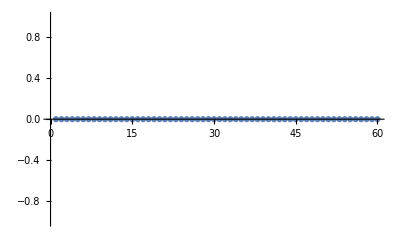

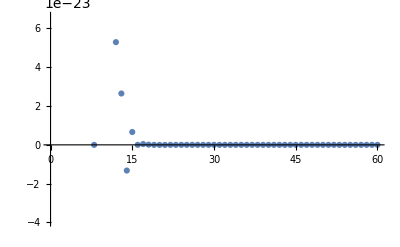

-Graphics-

```mathematica
ListPlot[Table[dlEdwxdat[ω],{ω,1,60}]]
ListPlot[Table[dlEdwydat[ω],{ω,1,60}]]
ListPlot[Table[dlEdwzdat[ω],{ω,1,60}]]
```

```mathematica
Re
```

```mathematica
L1=1.;
L2=1.;
M1=-1.;
M2=0.;
ww=15;
IEStr[L1,L2,M1,M2,ww]
datIEStr[L1,L2,M1,M2,ww]
IECCfr[L1,L2,M1,M2,ww]
CC[L1,M1,ww]*DD[L2,M2,ww]*
```

1.70958×10^-40+7.56629×10^-9 ⅈ

1.70958×10^-40+7.56629×10^-9 ⅈ

1.70958×10^-40+7.56629×10^-9 ⅈ

9.77759×10^-11-7.17465×10^-43 ⅈ

```mathematica
dlEdwx[10]//Quiet//Timing
```

{0.189558,0.+0. ⅈ}

```mathematica
dlEdwxdat[10]//Timing
```

{0.105373,0.+0. ⅈ}

```mathematica
NIntegrate[(LegendreP[1,-1,x]*LegendreP[1,0,x])/(√(1-x^2)),{x,-1,1}]
```

0.

```mathematica
ll1=1;
mm1=-1;
ll2=1;
mm2=-1;
DD[ll1,mm1]*DD[ll2,mm2]*
CC[ll1,mm1]*DD[ll2,mm2]*
DD[ll1,mm1]*CC[ll2,mm2]*
```

4.00589×10^-6+0. ⅈ

-7.70934×10^-7+0. ⅈ

-7.70934×10^-7+0. ⅈ

```mathematica
SphericalBesselJ[1,10]
```

SphericalBesselJ[1,10]

```mathematica
N[SphericalBesselJ[1,10]]
```

0.0784669

```mathematica
II[0,0,0]
```

II[0,0,0]

```mathematica
ll=2;
mm=0;
jj=0.;
II[ll,mm,jj,ll-jj]
```

0.666667

```mathematica
Mod[2,4]
```

2

```mathematica
A[1,0]
```

5.07771+0. ⅈ